In 8.09, you are welcome to use programs like Mathematica or Matlab when appropriate. Note, however, that this doesn’t mean every problem requires Mathematica and you should always try to think if you’re finding the solution in the simplest way. You should also make sure you note intermediate steps when you use Mathematica
This notebook introduces some of the concepts in Mathematica that you might find helpful. It only contains the basic information for each section and you should consult Mathematica documentation for further study.

To open each section, click the square bracket with an arrow to the far right of the title (for more info on how to format things like this, look athttp://reference.wolfram.com/language/howto/DoBasicNotebookStylingAndFormatting.html)

## Basics

### Syntax

When something isn’t working, it can be useful to quit your kernel and start fresh. You can also clear individual variable names as needed.

```mathematica
Quit[]
ClearAll[variable]
```

Variables get assigned using = sign. Arithmetic works as you would expect and functions take arguments with square brackets

```mathematica
variable=2+3*Sin[Pi/4]; (*Semicolon suppresses the output*)
```

```mathematica
variable
```

2+3/(√2)

Lists are contained in curly brackets. Mathematica starts counting at 1

```mathematica
list={1,4,a,dog,{42,dan}}
```

{1,4,a,dog,{42,dan}}

```mathematica
list[[1]]
```

1

```mathematica
list[[5,1]]
```

42

N[x] forces numerical values in x wherever possible

```mathematica
N[4/3*x+list[[1]]]
```

1.+1.33333 x

Simplify will reduce complex expressions for you

```mathematica
D[Integrate[1/(x^3+1),x],x]
```

1/(3 (1+x))-(-1+2 x)/(6 (1-x+x^2))+2/(3 (1+1/3 (-1+2 x)^2))

```mathematica
Simplify[%+Sin[x]^2+Cos[x]^2] (*% indicates the previous output*)
```

(2+x^3)/(1+x^3)

### Formulas

The syntax to define a function is simply functionname[variables_] := function. Note the colon before the equals sign, this is important as it tells Mathematica to reevaluate the function every time it is called.

```mathematica
f[x_]:=x^2+1;
g[x_,y_]:=x*y/Tan[x+y];
h[{x_,y_}]:=x^y;
```

```mathematica
f[1]
```

2

```mathematica
g[4,3]
```

12 Cot[7]

```mathematica
h[4,3]
```

h[4,3]

```mathematica
h[{4,3}]
```

64

### Derivatives

In order to take a derivative, you just use the syntax D[f,x]. To take the nth derivative, use D[f,{x,n}]. If f is just a function of x, you can use f’[x]

```mathematica
D[f[x],x]
```

2 x

```mathematica
f'[x]
```

2 x

```mathematica
D[h[{x,y}],x]
```

x^(-1+y) y

```mathematica
h'[{x,y}]
```

h'[{x,y}]

### Integrals

When taking integrals, you can either do it analytically, using Integrate[f,x] or Integrate[f,{x,x1,x2}], or you can do it numerically, using NIntegrate[f,{x,x1,x2}]

```mathematica
Integrate[f[x],x] (*Note that this doesn't include the constant that we know is there*)
```

x+x^3/3

```mathematica
Integrate[f[x],{x,x1,x2}]
```

-x1-x1^3/3+x2+x2^3/3

```mathematica
Integrate[g[x,y],x] (*Mathematica is powerful!*)
```

1/2 y (ⅈ π x+x^2 Cot[y]+π Log[1+ⅇ^(-2 ⅈ x)]+2 x Log[1-ⅇ^(2 ⅈ (x+ArcTan[Tan[y]]))]-π Log[Cos[x]]+2 ArcTan[Tan[y]] (-ⅈ x+Log[1-ⅇ^(2 ⅈ (x+ArcTan[Tan[y]]))]-Log[Sin[x+ArcTan[Tan[y]]]])-ⅈ PolyLog[2,ⅇ^(2 ⅈ (x+ArcTan[Tan[y]]))]-ⅇ^(ⅈ ArcTan[Tan[y]]) x^2 Cot[y] √(Sec[y]^2))

```mathematica
NIntegrate[h[{x,2x}],{x,1,2}]
```

4.91016

### Expansions

It can be useful to expand a function in a small parameter. Mathematica can do this to any order you like using Series[f,{x,x0,n}].

```mathematica
Series[Log[x],{x,1,5}]
```

(x-1)-1/2 (x-1)^2+1/3 (x-1)^3-1/4 (x-1)^4+1/5 (x-1)^5+O[x-1]^6

```mathematica
Series[g[x,y],{x,0,4}]
```

y Cot[y] x+(-y-y Cot[y]^2) x^2+(y Cot[y]+y Cot[y]^3) x^3+(-y/3-4/3 y Cot[y]^2-y Cot[y]^4) x^4+O[x]^5

### Matrices

Matrices in Mathematica are just lists, but have a lot of nice functionality. First we will just define a Matrix using basic list syntax. MatrixForm will display it nicely.

```mathematica
A={{1,0,0},{0,0,2},{0,1,0}}
```

{{1,0,0},{0,0,2},{0,1,0}}

```mathematica
MatrixForm[A]
```

(1 | 0 | 0
0 | 0 | 2
0 | 1 | 0)

We can also define matrices formulaically using Table

```mathematica
B=Table[i+j+1,{i,1,3},{j,1,3}]
```

{{3,4,5},{4,5,6},{5,6,7}}

```mathematica
MatrixForm[B]
```

(3 | 4 | 5
4 | 5 | 6
5 | 6 | 7)

Mathematica has a lot of built in functions for Matrices, some of which are shown here

```mathematica
Transpose[A](*Take the Transpose*)
```

{{1,0,0},{0,0,1},{0,2,0}}

```mathematica
Det[A](*Take the determinant*)
```

-2

```mathematica
Tr[B](*Take the trace*)
```

15

```mathematica
A.B(*Take the product of two matrices*)
```

{{3,4,5},{10,12,14},{4,5,6}}

```mathematica
Eigenvalues[A](*Get the eigenvalues*)
```

{-√2,√2,1}

```mathematica
Eigenvectors[B](*Get the eigenvectors*)
```

{{(2 (16+√249))/(47+3 √249),-(-79-5 √249)/(2 (47+3 √249)),1},{(2 (-16+√249))/(-47+3 √249),-(79-5 √249)/(2 (-47+3 √249)),1},{1,-2,1}}

## Solving Equations

### Basic Equation Solving

An equation in Mathematica is written with a double equals sign (==). The Solve, NSolve and FindRoot functions will all solve equations, with slightly different applications.

Solve[equations, variables] will find equation solutions analytically. It returns a list of “replacement rules”, which can be applied using the synax “/.”.

```mathematica
quadraticsolution=Solve[x^2+a*x-b==0,x]
```

{{x→1/2 (-a-√(a^2+4 b))},{x→1/2 (-a+√(a^2+4 b))}}

```mathematica
x/.quadraticsolution
```

{1/2 (-a-√(a^2+4 b)),1/2 (-a+√(a^2+4 b))}

```mathematica
x/.quadraticsolution[[1]]
```

1/2 (-a-√(a^2+4 b))

```mathematica
Solve[{(x+y)^2-a*x-b*y==0,y==x},{x,y}]
```

{{x→0,y→0},{x→(a+b)/4,y→(a+b)/4}}

NSolve[equation, variables] will find equation solutions numerically. It also returns a list of “replacement rules”.

```mathematica
Nquadraticsolution=NSolve[x^2+5.5*x-6.0==0,x]
```

{{x→-6.43273},{x→0.93273}}

```mathematica
x/.Nquadraticsolution
```

{-6.43273,0.93273}

```mathematica
x/.Nquadraticsolution[[1]]
```

-6.43273

```mathematica
NSolve[{(x+y)^2-3*x-4*y==0,y==x},{x,y}]
```

{{x→1.75,y→1.75},{x→0.,y→0.}}

Finally, FindRoot[equation,{x,x0}] will find a numerical solution close to x0. It is very fast compared to the other two.

```mathematica
Nquadraticsolution=FindRoot[x^2+5.5*x-6.0==0,{x,1}]
```

{x→0.93273}

```mathematica
x/.Nquadraticsolution
```

0.93273

```mathematica
x/.Nquadraticsolution[[1]]
```

0.93273

```mathematica
FindRoot[{(x+y)^2-3*x-4*y==0,y==x},{{x,1},{y,0}}]
```

{x→-7.18717×10^-16,y→-7.18717×10^-16}

### Solving Differential Equations

Solving differential equations can be done analytically with DSolve[eqn, y[x], x] or numerically with NDSolve[eqn,y[x],{x,xmin,xmax}]. In both of these, y is the function you are solving for and x is the independent variable. Once again, the results will be stored as replacement rules.

```mathematica
DSolve[y'[x]+y[x]==a*Sin[x],y[x],x]
```

{{y[x]→ⅇ^-x C[1]+1/2 a (-Cos[x]+Sin[x])}}

```mathematica
NDSolve[y'[x]+y[x]==Sin[x],y[x],{x,0,2}] (*This should throw an error*)
```

NDSolve::ndnco: The number of constraints (0) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (1).

NDSolve[y[x]+y'[x]==Sin[x],y[x],{x,0,2}]

```mathematica
(*With NDSolve, we need to specify boundary conditions*)
NDSolve[{y'[x]+y[x]==Sin[x],y[1]==1},y[x],{x,0,2}]
```

{{y[x]→InterpolatingFunction[{{0., 2.}}, <>][x]}}

## Plotting

A basic function of one variable is plotted using Plot[f[x],{x,xmin,xmax}]

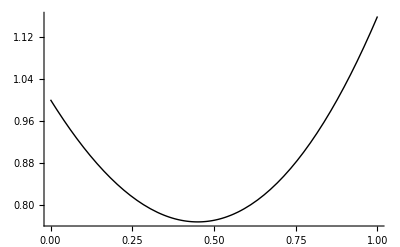

```mathematica
Plot[1+x^2-Sin[x],{x,0,1}]
```

You can also plot several functions at once with Plot[{f1[x],f2[x],f3[x]...},{x,xmin,xmax}]

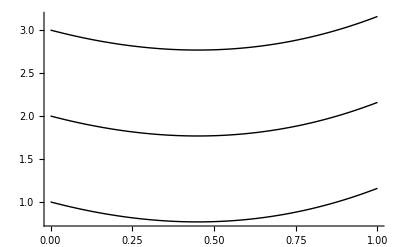

```mathematica
Plot[{1+x^2-Sin[x],2+x^2-Sin[x],3+x^2-Sin[x]},{x,0,1}]
```

There are many options that you can use when plotting, especially for formatting. For full information, refer to the Documentation.

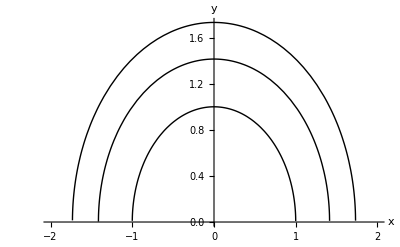

```mathematica
Plot[{Sqrt[1-x^2],Sqrt[2-x^2],Sqrt[3-x^2]},{x,-2,2},PlotStyle->{{Thick,Red},{Dashed,Green},{Thin,Blue}},AxesLabel->{"x","y"}]
```

Here is a more complicated example of plotting a solution to a differential equation with several parameter choices

```mathematica
plotsolution=DSolve[{y'[x]==a*Sin[x],y[0]==2},y[x],x]
```

{{y[x]→2+a-a Cos[x]}}

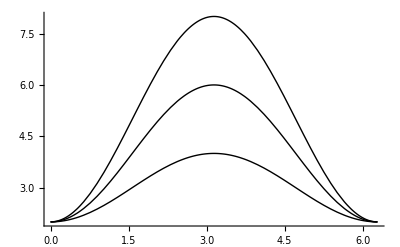

```mathematica
Plot[{y[x]/.plotsolution[[1]]}/.{a->{1,2,3}},{x,0,2*Pi}]
```

## Lagrangian Example - Elastic Pendulum (Section 1)

We derived the Lagrangian for an elastic pendulum in recitation. Here, we will get the Euler Lagrange equations and solve them numerically

```mathematica
(*First we define the Lagrangian, using xp and thetap as stand ins for the derivatives*)
LelasticPendulum[theta_,thetap_,x_,xp_]:=1/2*m*(xp^2+(l+x)^2*thetap^2)+m*g*(l+x)*Cos[theta]-1/2*k*x^2;
```

```mathematica
(*Here we take the appropriate derivatives to get our EL equations for x and theta*)
ELequationx=Simplify[D[D[LelasticPendulum[theta,thetap,x,xp],xp],x]*xp+D[D[LelasticPendulum[theta,thetap,x,xp],xp],theta]*thetap+D[D[LelasticPendulum[theta,thetap,x,xp],xp],xp]*xpp+D[D[LelasticPendulum[theta,thetap,x,xp],xp],thetap]*thetapp-D[LelasticPendulum[theta,thetap,x,xp],x]]/.{theta->θ[t],thetap->θ'[t],thetapp->θ''[t],x->x[t],xp->x'[t],xpp->x''[t]}

ELequationθ=Simplify[D[D[LelasticPendulum[theta,thetap,x,xp],thetap],x]*xp+D[D[LelasticPendulum[theta,thetap,x,xp],thetap],theta]*thetap+D[D[LelasticPendulum[theta,thetap,x,xp],thetap],xp]*xpp+D[D[LelasticPendulum[theta,thetap,x,xp],thetap],thetap]*thetapp-D[LelasticPendulum[theta,thetap,x,xp],theta]]/.{theta->θ[t],thetap->θ'[t],thetapp->θ''[t],x->x[t],xp->x'[t],xpp->x''[t]}
```

-g m Cos[θ[t]]+k x[t]-m (l+x[t]) θ'[t]^2+m x''[t]

m (l+x[t]) (g Sin[θ[t]]+2 x'[t] θ'[t]+(l+x[t]) θ''[t])

```mathematica
(*Let's substitute in some numbers so we can solve numerically*)
ELequationxNum=Evaluate[ELequationx/.{l->1,g->1,m->1,k->4}]
ELequationθNum=Evaluate[ELequationθ/.{l->1,g->1,m->1,k->4}]
```

-Cos[θ[t]]+4 x[t]-(1+x[t]) θ'[t]^2+x''[t]

(1+x[t]) (Sin[θ[t]]+2 x'[t] θ'[t]+(1+x[t]) θ''[t])

```mathematica
(*Use NDSolve to get the numerical solutions to our differential equations*)
numericalElasticSolution=NDSolve[{ELequationxNum==0,ELequationθNum==0,θ[0]==Pi/6,θ'[0]==0,x[0]==0,x'[0]==.2},{θ[t],x[t]},{t,0,100}]
```

{{θ[t]→InterpolatingFunction[…][t],x[t]→InterpolatingFunction[…][t]}}

```mathematica
(*Create a nice graphic for seeing the results*)
masswithspring[tt_]:=Module[{localθ=((θ[t]/.numericalElasticSolution)/.{t->tt})[[1]],localx=((x[t]/.numericalElasticSolution)/.{t->tt})[[1]]},Graphics[{Thickness[.05/(1+localx)],Black,Line[{{0,0},{(1+localx)*Sin[localθ],-(1+localx)*Cos[localθ]}}],Red,Disk[{(1+localx)*Sin[localθ],-(1+localx)*Cos[localθ]},0.1]},Axes->True,PlotRange->{{-1,1},{0,-2}}]]
```

```mathematica
(*Show the results over time*)
Animate[masswithspring[tt],{tt,0,100},AnimationRate->1]
```

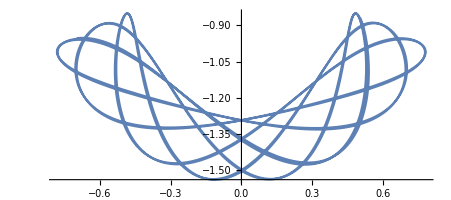

```mathematica
(*Plot the path that the mass takes over time*)
ParametricPlot[Module[{localθ=((θ[t]/.numericalElasticSolution)/.{t->tt})[[1]],localx=((x[t]/.numericalElasticSolution)/.{t->tt})[[1]]},{(1+localx)*Sin[localθ],-(1+localx)*Cos[localθ]}],{tt,0,50}]
```

## Hamiltonian Example - Particle on a Cylinder with Central Force (Section 2)

In recitation, we derived that the motion for a particle on a cylinder with a central force F=-kr is just harmonic in the z direction and moves with a constant angular momentum in the θ direction. Here we will plot that

```mathematica
PlotCylindricalMotion[ω_,thetav_,t_]:=Show[Graphics3D[{Blue,Opacity[0.2],Cylinder[{{0,0,-1},{0,0,1}},1],Red,Opacity[1],Sphere[{Cos[thetav*t],Sin[thetav*t],Cos[ω*t]},0.1]},PlotRange->{{-1.2,1.2},{-1.2,1.2},{-1.2,1.2}}],ParametricPlot3D[{Cos[thetav*tt],Sin[thetav*tt],Cos[ω*tt]},{tt,0,t},PlotStyle->{Black}]];
```

```mathematica
Animate[PlotCylindricalMotion[Pi,1,t],{t,0,100},AnimationRate->1]
```